```mathematica
theo={214.343,142.895};
```

### 1. Isotop

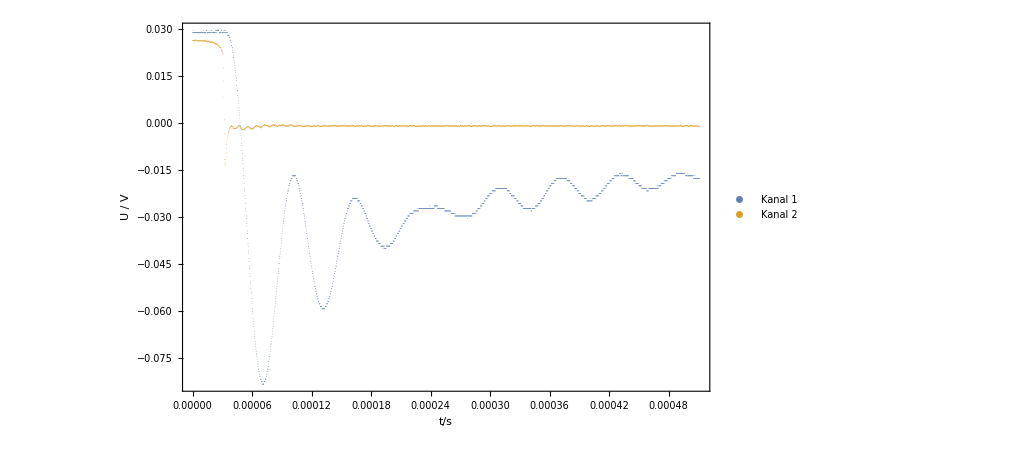

```mathematica
path = "./02-63.7mA-085mA.tab";
ch1zoom = 1;
ch2zoom = 1;
SetDirectory[NotebookDirectory[]];
data = Drop[Import[path], 1];
ch1 = Transpose[{data[[All,1]],data[[All,2]]*ch1zoom}];
ch2 = Transpose[{data[[All,1]],data[[All,3]]*ch2zoom}];
ListPlot[{ch1, ch2}, PlotRange->All, Frame->True, ImageSize->750, PlotStyle->{PointSize[0.0001]}, PlotLegends->{"Kanal 1"<>If[ch1zoom ≠ 1, " x "<>ToString[ch1zoom], ""], "Kanal 2"<>If[ch2zoom ≠ 1, " x "<>ToString[ch2zoom], ""]}, FrameLabel->{"t/s", "U / V"}]
```

{0.,4.38,8.76,13.14,17.52,21.9,26.28,30.66,32.85,35.04,37.23,38.106,39.42,41.61,43.8}

{0.00003966,0.00004471,0.00004564,0.00004548,0.00013968,0.00015341,0.00013171,0.00020211,0.00029325,0.00030403,0.00033,0.0003193,0.0003162,0.00031853,0.00029942}

{4.9575,5.58875,6.52,7.58,9.312,11.8008,14.6344,22.4567,29.325,43.4329,66.,63.86,63.24,45.5043,33.2689}

| Estimate | Standard Error | t-Statistic | P-Value
a | 207.842 | 3.88418 | 53.5099 | 1.39761×10^-12
b | 40.2133 | 0.13902 | 289.262 | 3.58966×10^-19

18.6505

1.6955

| Estimate | Standard Error | t-Statistic | P-Value
a | 222.217 | 9.26027 | 23.9968 | 1.64681×10^-11
b | 38.6628 | 0.170193 | 227.171 | 3.56122×10^-23
c | 2.46697 | 0.252069 | 9.78688 | 4.51766×10^-7

52.2067

3.48045

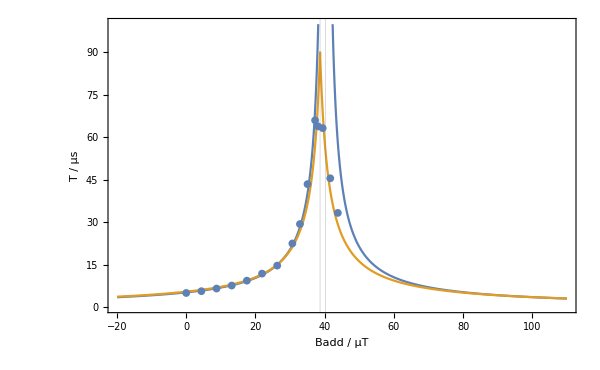

```mathematica
maxpos={{{2.513*^-5,-0.003139},{6.479*^-5,-0.007048}},{{2.697*^-5,-0.003181},{7.168*^-5,-0.008716}},{{2.283*^-5,-0.003121},{6.847*^-5,-0.01225}},{{2.513*^-5,-0.003689},{7.061*^-5,-0.01443}},{{4.842*^-5,-0.00981},{0.0001881,-0.01686}},{{4.199*^-5,-0.004052},{0.0001954,-0.02148}},{{4.689*^-5,-0.0112},{0.0001786,-0.02577}},{{5.979*^-5,-0.01918},{0.0002619,-0.02337}},{{6.975*^-5,-0.02752},{0.000363,-0.03039}},{{8.277*^-5,-0.02019},{0.0003868,-0.01651}},{{0.0001027,-0.01676},{0.0004327,-0.01618}},{{0.0001057,-0.01052},{0.000425,-0.01438}},{{0.0001004,-0.02238},{0.0004166,-0.02831}},{{8.047*^-5,-0.03606},{0.000399,-0.03358}},{{6.898*^-5,-0.01933},{0.0003684,-0.01838}}};
maxnum={8,8,7,6,15,13,9,9,10,7,5,5,5,7,9};
current={0,10,20,30,40,50,60,70,75,80,85,87,90,95,100};
B=0.438current
maxdiff=Table[maxpos[[i,2,1]]-maxpos[[i,1,1]],{i,1,Length[maxpos]}]
T=maxdiff/maxnum*10^6
plotdata=Transpose[{B,T}];
fitdata1=Drop[plotdata,-4];
Terrors1=Drop[0.03T,-4];
fitdata2=plotdata;
Terrors2=0.05T;
nlm1=NonlinearModelFit[fitdata1,{a/Abs[b-x],{0<a,0<b,b<100}},{{a,200},{b,39}},x,Weights->1/Terrors1^2];
Quiet[nlm1["ParameterTable"]]
χ1=Sum[((nlm1[fitdata1[[n,1]]]-fitdata1[[n,2]])/Terrors1[[n]])^2,{n,1,Length[fitdata1]}]
%/Length[fitdata1]


nlm2=NonlinearModelFit[fitdata2,{a/(Abs[b-x]+c),{0<a,0<b,b<100,1<c,c<20}},{{a,200},{b,38},{c,3}},x,Weights->1/Terrors2^2];
Quiet[nlm2["ParameterTable"]]
χ2=Sum[((nlm2[fitdata2[[n,1]]]-fitdata2[[n,2]])/Terrors2[[n]])^2,{n,1,Length[fitdata2]}]
%/Length[fitdata2]


Quiet[Show[Plot[{Normal[nlm1],Normal[nlm2]},{x,-20,110},PlotRange->{{-20,110},{0,100}},Frame->True,FrameLabel->{"Badd / µT","T / µs"},GridLines->{{nlm1["ParameterTableEntries"][[2,1]],nlm2["ParameterTableEntries"][[2,1]]},{}},ImageSize->600],ListPlot[plotdata,PlotMarkers->{Automatic,8}]]]
```

### 2. Isotop

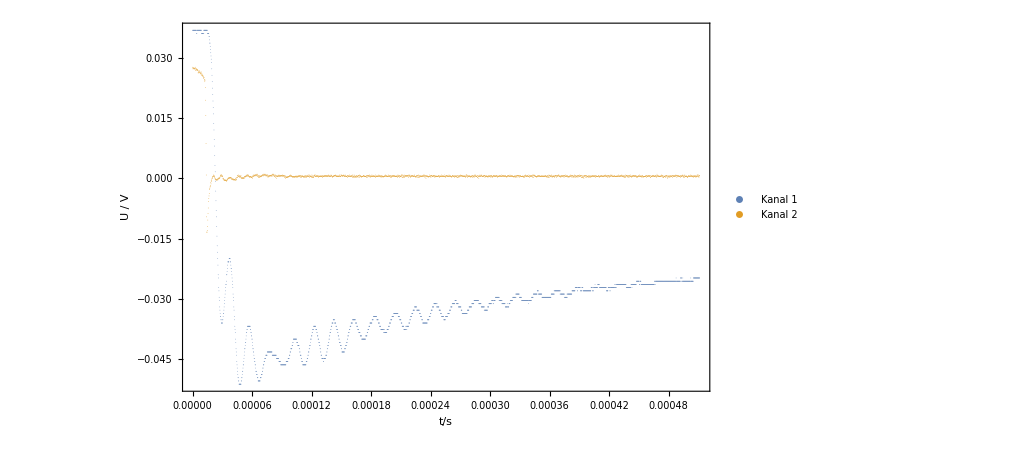

```mathematica
path = "./03-64.1mA-100mA.tab";
ch1zoom = 1;
ch2zoom = 1;
SetDirectory[NotebookDirectory[]];
data = Drop[Import[path], 1];
ch1 = Transpose[{data[[All,1]],data[[All,2]]*ch1zoom}];
ch2 = Transpose[{data[[All,1]],data[[All,3]]*ch2zoom}];
ListPlot[{ch1, ch2}, PlotRange->All, Frame->True, ImageSize->750, PlotStyle->{PointSize[0.0001]}, PlotLegends->{"Kanal 1"<>If[ch1zoom ≠ 1, " x "<>ToString[ch1zoom], ""], "Kanal 2"<>If[ch2zoom ≠ 1, " x "<>ToString[ch2zoom], ""]}, FrameLabel->{"t/s", "U / V"}]
```

{0.,4.38,8.76,13.14,17.52,21.9,26.28,30.66,32.85,35.04,37.23,37.668,39.42,41.61,43.8}

{0.00001945,0.00002243,0.00002565,0.00006693,0.00006922,0.00011735,0.00012958,0.00013075,0.00018837,0.00023893,0.00035761,0.00031935,0.00043031,0.00032692,0.00029177}

{3.24167,3.73833,4.275,5.14846,6.29273,7.82333,10.7983,14.5278,18.837,29.8662,44.7013,45.6214,43.031,29.72,20.8407}

| Estimate | Standard Error | t-Statistic | P-Value
a | 138.847 | 3.22449 | 43.0603 | 9.80786×10^-12
b | 40.1773 | 0.171189 | 234.695 | 2.35527×10^-18

28.9227

2.62933

| Estimate | Standard Error | t-Statistic | P-Value
a | 143.497 | 4.2698 | 33.6074 | 3.05916×10^-13
b | 38.4378 | 0.115425 | 333.01 | 3.61951×10^-25
c | 2.12613 | 0.171369 | 12.4067 | 3.33278×10^-8

26.4817

1.76545

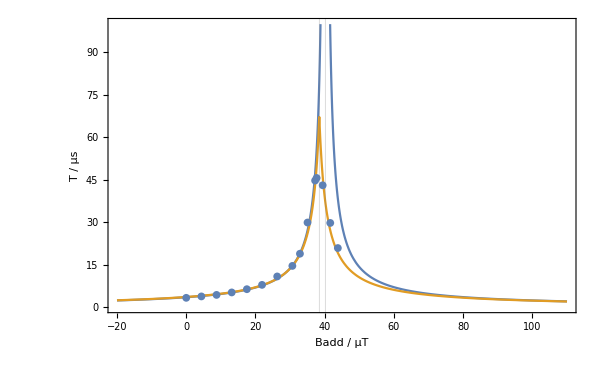

```mathematica
maxpos={{{2.589*^-5,-0.00862},{4.534*^-5,-0.0145}},{{2.39*^-5,-0.0091},{4.633*^-5,-0.01698}},{{2.198*^-5,-0.01118},{4.763*^-5,-0.02489}},{{3.018*^-5,-0.02426},{9.711*^-5,-0.03372}},{{2.865*^-5,-0.0276},{9.787*^-5,-0.04458}},{{3.525*^-5,-0.01576},{0.0001526,-0.0197}},{{3.372*^-5,-0.01733},{0.0001633,-0.02318}},{{4.475*^-5,-0.02892},{0.0001755,-0.03193}},{{5.903*^-5,-0.03202},{0.0002474,-0.02893}},{{4.907*^-5,-0.01593},{0.000288,-0.01993}},{{6.439*^-5,-0.0176},{0.000422,-0.02425}},{{6.515*^-5,-0.01756},{0.0003845,-0.02736}},{{6.209*^-5,-0.01848},{0.0004924,-0.01959}},{{4.678*^-5,-0.02398},{0.0003737,-0.02595}},{{5.673*^-5,-0.0369},{0.0003485,-0.02826}}};
maxnum={6,6,6,13,11,15,12,9,10,8,8,7,10,11,14};
current={0,10,20,30,40,50,60,70,75,80,85,86,90,95,100};
B=0.438current
maxdiff=Table[maxpos[[i,2,1]]-maxpos[[i,1,1]],{i,1,Length[maxpos]}]
T=maxdiff/maxnum*10^6
plotdata=Transpose[{B,T}];
fitdata1=Drop[plotdata,-4];
Terrors1=Drop[0.03T,-4];
fitdata2=Drop[plotdata,-0];
Terrors2=Drop[0.05T,-0];
nlm1=NonlinearModelFit[fitdata1,{a/Abs[b-x],{0<a,0<b,b<100}},{{a,140},{b,39}},x,Weights->1/Terrors1^2];
Quiet[nlm1["ParameterTable"]]
χ1=Sum[((nlm1[fitdata1[[n,1]]]-fitdata1[[n,2]])/Terrors1[[n]])^2,{n,1,Length[fitdata1]}]
%/Length[fitdata1]


nlm2=NonlinearModelFit[fitdata2,{a/(Abs[b-x]+c),{0<a,0<b,b<45,1<c,c<20}},{{a,140},{b,37},{c,3}},x,Weights->1/Terrors2^2];
Quiet[nlm2["ParameterTable"]]
χ2=Sum[((nlm2[fitdata2[[n,1]]]-fitdata2[[n,2]])/Terrors2[[n]])^2,{n,1,Length[fitdata2]}]
%/Length[fitdata2]


Quiet[Show[Plot[{Normal[nlm1],Normal[nlm2]},{x,-20,110},PlotRange->{{-20,110},{0,100}},Frame->True,FrameLabel->{"Badd / µT","T / µs"},GridLines->{{nlm1["ParameterTableEntries"][[2,1]],nlm2["ParameterTableEntries"][[2,1]]},{}},ImageSize->600],ListPlot[plotdata,PlotMarkers->{Automatic,8}]]]
```

### Winkelberechnung

```mathematica
func[VarsW_]:=ArcSin[a/b]*180/π

VarsW:={a,b}
Werte:={Quiet[nlm2["ParameterTableEntries"]][[3,1]],Quiet[nlm2["ParameterTableEntries"]][[2,1]]}
Fehler:={Quiet[nlm2["ParameterTableEntries"]][[3,2]],Quiet[nlm2["ParameterTableEntries"]][[2,2]]}

VarsF:=Table[ToExpression["s"<>ToString[VarsW[[i]] ] ],{i,1,Length[VarsW]}]
RepList:=Join[
Table[VarsW[[i]]->Werte[[i]],{i,1,Length[VarsW]}],
Table[VarsF[[i]]->Fehler[[i]],{i,1,Length[VarsW]}]]
NullList:=Table[
If[Count[Flatten[{Fehler[[i]]}],0]==Length[Flatten[{Fehler[[i]]}]],
VarsF[[i]]->0,
VarsF[[i]]->VarsF[[i]]],
{i,1,Length[VarsW]}]


erg=func[VarsW]/.RepList//N
ergF=√Sum[(D[func[VarsW],{VarsW}][[i]]*VarsF[[i]] )^2,{i,1,Length[VarsW]}]/.RepList//N
relF=(100*ergF)/erg//N
FullSimplify[√Sum[(D[func[VarsW],{VarsW}][[i]]*VarsF[[i]] )^2,{i,1,Length[VarsW]}]/.NullList,Flatten[{VarsW,VarsF}]∈Reals](*/.Table[VarsF[[i]]->Subscript[s, VarsW[[i]]],{i,1,Length[VarsW]}]*)
```

3.17085

0.256013

8.07397

(180 √((b^2 sa^2+a^2 sb^2)/(-a^2 b^2+b^4)))/π